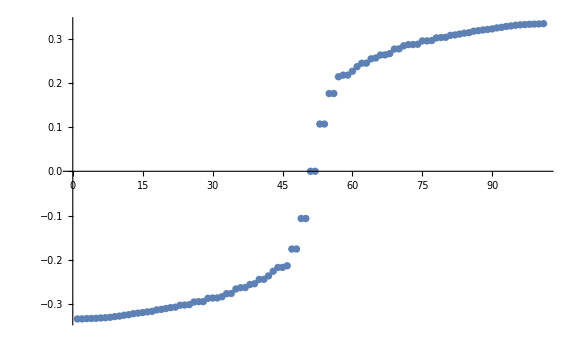

{{12,36},{36,12}}

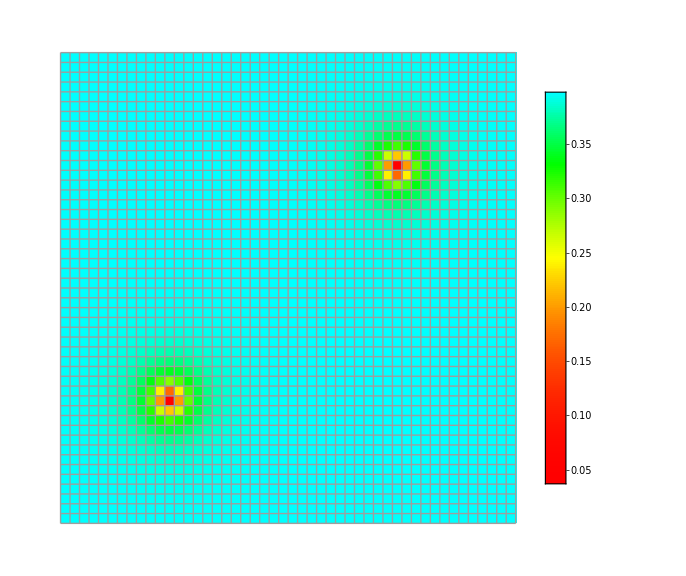

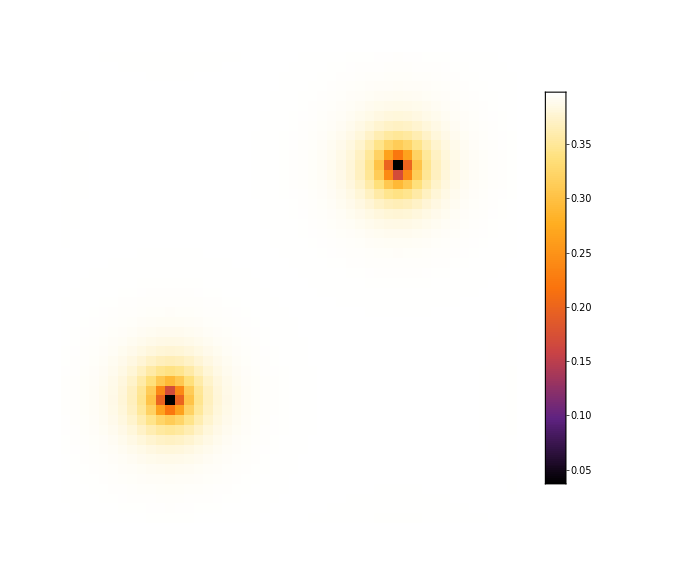

```mathematica
SetDirectory[NotebookDirectory[]];
xn=yn=48;
energy = Flatten[Import["energy.dat"]];
del = Flatten[Import["order_module.dat"]];
ListPlot[energy[[Round[Length[energy]/2]-50;;Round[Length[energy]/2]+50]],ImageSize->Large]
del2=ArrayReshape[del,{48,48}];
Export["del.dat",del2];
Position[del2,n_/;n<(Min[del2]+0.1)]
ArrayPlot[del2,ColorFunction->(Hue[#^2/2]&),PlotLegends->Automatic,PlotTheme->"Detailed",ImageSize->Large,Mesh->All]
ArrayPlot[del2,ColorFunction->"SunsetColors",PlotLegends->Automatic,PlotTheme->"Detailed",ImageSize->Large]
```